```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
c={0.5,0.5};
a=0.2;
b=0.1;
```

```mathematica
xref[s_]:=c+{a Cos[2π s]/(1+Cos[2π s]^2),b Sin[2 π s]}
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/monolithic/solution/snapshots/csv/dyds.csv"]
```

```mathematica
plotdydsrefnum = Graphics[
  {
   {Yellow, Arrowheads[0.02],AbsoluteThickness[3],
    Table[Arrow[{{t[[i,3]],t[[i,4]]}, {t[[i,3]],t[[i,4]]} + 0.03{t[[i,1]],t[[i,2]]}}],{i, 1, Length[t]}]}
   },
  Axes -> True, AspectRatio -> Automatic
 ]
```

-Graphics-

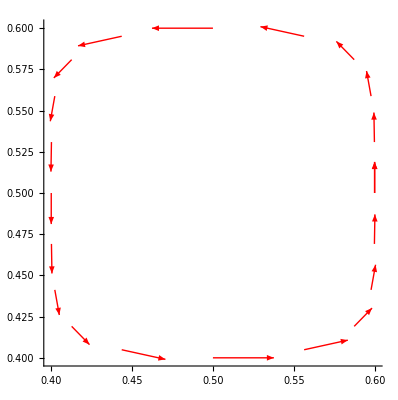

```mathematica
plotdydsref = Graphics[
  {
   (* normal vectors at sample points *)
   {Red, Arrowheads[0.02],
    Table[Arrow[{xref[s], xref[s] + 0.03 xref'[s]}], {s, 0, 1, 0.05}]}
   },
  Axes -> True, AspectRatio -> Automatic
 ]
```

```mathematica
Show[plotdydsrefnum,plotdydsref,PlotRange->Full]
```

-Graphics-